## For One Site Fermionic Hubbard Model

## For Strong Coupling (t = 0)

### Plot of ρ vs μ

```mathematica
Clear[ρ]
Clear[β]
Clear[μ]
Clear[U]
partitionFunctionZ[U_, T_, μ_]:= Exp[-(1/T)*(U/4)]+2*Exp[-(1/T)*(-μ-(U/4))]+Exp[-(1/T)*(-2*μ+(U/4))]
ρ[U_, T_, μ_]:= 2(Exp[-(1/T)*(-μ-(U/4))]+Exp[-(1/T)*(-2*μ+(U/4))])/(partitionFunctionZ[U, T, μ])
```

```mathematica
(**p1 = Plot[ρ[4,2,μ ], {μ,-4,8},AxesLabel->{"μ","ρ"},PlotLabel->"ρ vs. μ", PlotStyle->Red]**)
p2 =  Plot[ρ[4,2,μ ], {μ,-6,6},PlotLabel->"ρ vs. μ (U = 4)", PlotStyle->Blue, PlotLegends->Placed[{"T=2"}, {Left, Top}],FrameLabel->{{"ρ",""},{"μ",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic];
p3  = Plot[ρ[4,0.5,μ ], {μ,-6,6},PlotLabel->"ρ vs. μ (U = 4)",PlotStyle->Red, PlotLegends->Placed[{"T=0.5"}, {Left, Top}], FrameLabel->{{"ρ",""},{"μ",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic];
p4 = Plot[ρ[4,0.25,μ ], {μ,-6,6},PlotLabel->"ρ vs. μ (U = 4)", PlotStyle->Orange, PlotLegends->Placed[{"T=0.25"}, {Left, Top}],FrameLabel->{{"ρ",""},{"μ",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic];
```

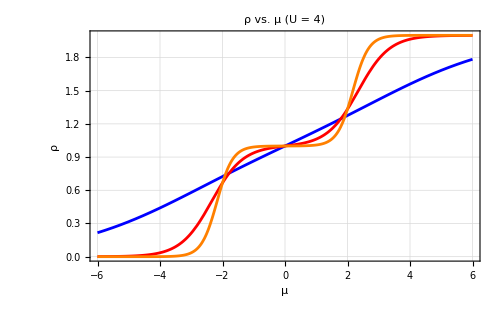

```mathematica
Show[p2, p3, p4, PlotRange->{{-6,6},{0,2}}]
```

### Plot of E and Specific Heat as function of T for U = 4

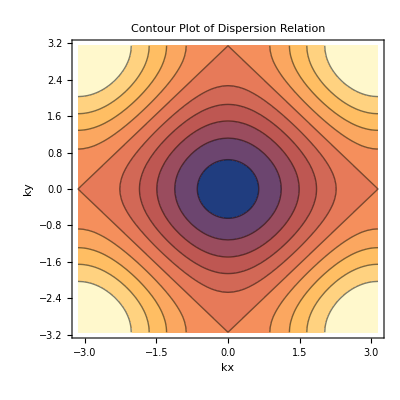

```mathematica
(*Energy Contour Plot for 2D Hubbard Model*)
t=1;
ContourPlot[-2*t*(Cos[kx]+Cos[ky]),{kx,-Pi,Pi},{ky,-Pi,Pi},PlotRange->All,ContourLabels->False,Contours->10,AxesLabel->{"kx","ky"},
PlotLabel->"Contour Plot of Dispersion Relation"]
```

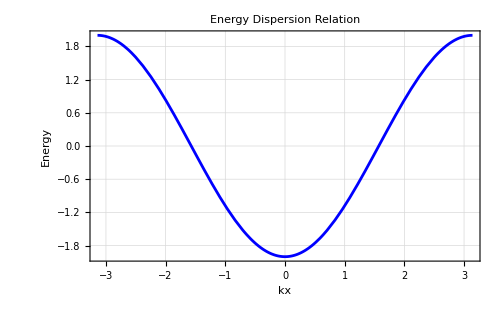

```mathematica
(*Energy Contour Plot for 2D Hubbard Model*)
t=1;
energydisp[kx_] := -2t*Cos[kx]
ed1 = Plot[energydisp[kx], {kx,  -Pi, Pi},PlotLabel->"Energy Dispersion Relation", PlotStyle->Blue,FrameLabel->{{"Energy",""},{"kx",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic]
```

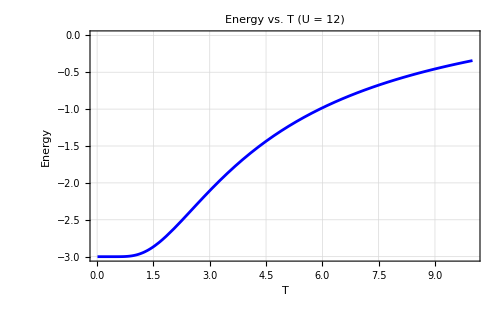

```mathematica
(*Energy vs. T for U = 8, μ = 0, t = 0 -> Half-filled Case*)
partitionFunctionZ[U_, T_, μ_]:= Exp[-(1/T)*(U/4)]+2*Exp[-(1/T)*(-μ-(U/4))]+Exp[-(1/T)*(-2*μ+(U/4))]
energy[U_, T_, μ_]:= (Exp[-(1/T)*(U/4)]*(2U/4)+2*Exp[-(1/T)*(-μ-(U/4))]*(1)*(-μ-(U/4))+Exp[-(1/T)*(-2*μ+(U/4))]*(1)*(-2μ+(U/4)))/(partitionFunctionZ[U, T, μ])
e1 =  Plot[energy[12,T,0 ], {T,0.01,10},PlotLabel->"Energy vs. T (U = 12)", PlotStyle->Blue,FrameLabel->{{"Energy",""},{"T",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic]
```

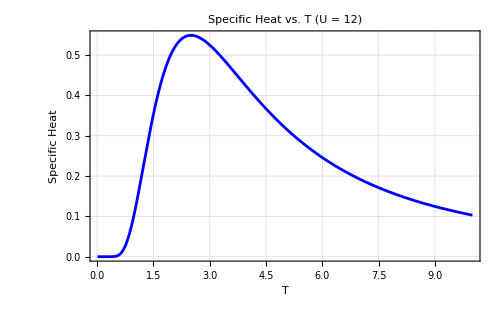

```mathematica
(*Specific Heat vs. T*)
partitionFunctionZ[U_, T_, μ_]:= Exp[-(1/T)*(U/4)]+2*Exp[-(1/T)*(-μ-(U/4))]+Exp[-(1/T)*(-2*μ+(U/4))]
energy[U_, T_, μ_]:= (Exp[-(1/T)*(U/4)]*(2U/4)+2*Exp[-(1/T)*(-μ-(U/4))]*(1)*(-μ-(U/4))+Exp[-(1/T)*(-2*μ+(U/4))]*(1)*(-2μ+(U/4)))/(partitionFunctionZ[U, T, μ])
specificHeat[12, T_, 0]:= Evaluate@D[energy[12, T, 0], {T,1}]
s1 = Plot[specificHeat[12,T,0 ], {T,0.01,10},PlotLabel->"Specific Heat vs. T (U = 12)", PlotStyle->Blue,FrameLabel->{{"Specific Heat",""},{"T",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic]
```

### Plot of Local Moment as a function of T and U at half-filling (μ = 0)

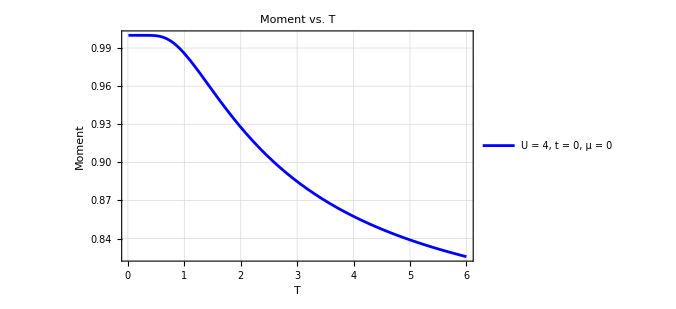

```mathematica
ρ[U_, T_, μ_]:= 2*(Exp[-(1/T)*(-μ-(U/4))]+2*Exp[-(1/T)*(-2*μ+(U/4))])/(Exp[-(1/T)*U/4]+(2*(Exp[-(1/T)*(-μ-(U/4))]))+ Exp[-(1/T)*(-2*μ+(U/4))])
magnetizationSquaredT[U_,T_,μ_]:=2*ρ[U,T,0] - (ρ[U,T,0]*ρ[U,T,0])
m2 = Plot[magnetizationSquaredT[4,T,0], {T,0.01,6},PlotLabel->"Moment vs. T", PlotLegends -> Placed[
   LineLegend[{"U = 4, t = 0, μ = 0"}],
   {Right, Top}], PlotStyle->Blue,FrameLabel->{{"Moment",""},{"T",""}},BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},
   Frame->True,ImageSize->500, GridLines->Automatic]
```

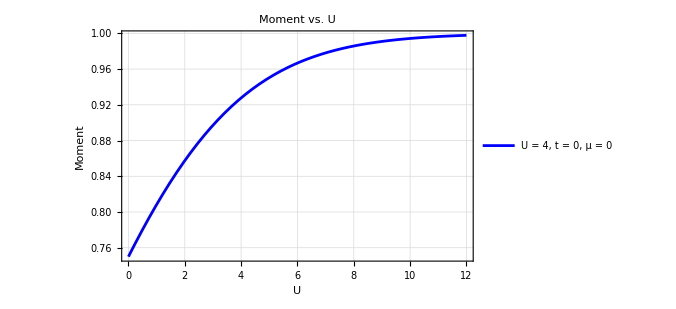

```mathematica
ρ[U_, β_, μ_]:= 2*(Exp[-β*(-μ-(U/4))]+2*Exp[-β*(-2*μ+(U/4))])/(Exp[-β*U/4]+(2*(Exp[-β*(-μ-(U/4))]))+ Exp[-β*(-2*μ+(U/4))])
magnetizationSquared[U_,β_,μ_]:=2*ρ[U,β,0] - (ρ[U,β,0]*ρ[U,β,0])
m1 = Plot[magnetizationSquared[U,0.5,0], {U,0,12},PlotLabel->"Moment vs. U", PlotStyle->Blue, PlotLegends -> Placed[
   LineLegend[{"U = 4, t = 0, μ = 0"}],
   {Left, Top}],
FrameLabel->{{"Moment",""},{"U",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, 
GridLines->Automatic]
```

QMBT H.W

```mathematica
Series[Tanh[b*Sqrt[ek*ek + de*de]],{ek,0,3}]
```

Tanh[b √(de^2)]+((b-b Tanh[b √(de^2)]^2) ek^2)/(2 √(de^2))+O[ek]^4

```mathematica
Integrate[Tanh[b*Sqrt[ek*ek + de*de]]/(Sqrt[ek*ek + de*de]), {ek, 0, wd}, Assumptions->{b>0, wd>0}]
```

Integrate[Tanh[b √(de^2+ek^2)]/(√(de^2+ek^2)),{ek,0,wd},Assumptions→{b>0,wd>0}]

```mathematica
Integrate[1/(Sqrt[ek^2+de0^2]),{ek,0,wd},Assumptions->{wd>0}]
```

ConditionalExpression[ArcTanh[wd/(√(de0^2+wd^2))], wd<Im[de0]||wd+Im[de0]<0||Re[de0]≠0]

## Non-interacting Limit (U = 0)

### Plot of Energy and Specific Heat vs. T for constant μ

```mathematica
Clear[t]
Eigenvalues[{{-μ,-t,0, -t},{-t,-μ,-t, 0},{0,-t,-μ, -t}, {-t, 0, -t, -μ}}]
```

{-2 t-μ,2 t-μ,-μ,-μ}

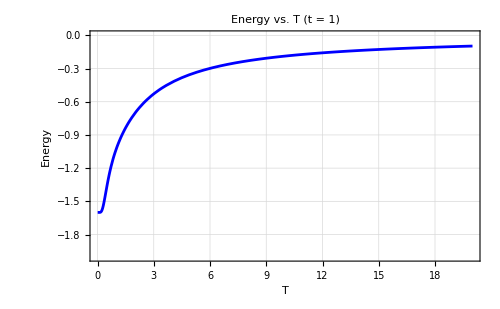

```mathematica
partitionF2[t_, T_, μ_]:=2Exp[-μ/T]+(Exp[-(2t-μ)/T])+ Exp[-(-2t-μ)/T]
energy2[t_, T_, μ_]:=-(Exp[(-1/T)*(-2t -μ)]*(-1)*(-2t-μ)+2Exp[-(1/T)*(-μ)]*(-μ)+Exp[(-1/T)*(2t -μ)]*(-1)*(2t-μ))/partitionF2[t, T, μ]
e2 =  Plot[energy2[1,T,-0.4], {T,0.01,20},PlotLabel->"Energy vs. T (t = 1)", 
PlotStyle->Blue,FrameLabel->{{"Energy",""},{"T",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},
Frame->True,ImageSize->500, GridLines->Automatic, PlotRange->{{0, 20}, {-2, 0}}]
```

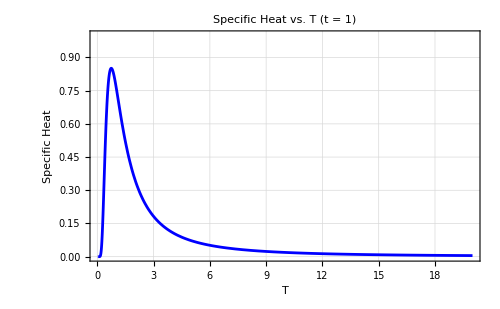

```mathematica
(*Specific Heat vs. T*)
partitionF2[t_, T_, μ_]:=2Exp[-μ/T]+(Exp[-(2t-μ)/T])+ Exp[-(-2t-μ)/T]
energy2[t_, T_, μ_]:=-(Exp[(-1/T)*(-2t -μ)]*(-1)*(-2t-μ)+2Exp[-(1/T)*(-μ)]*(-μ)+Exp[(-1/T)*(2t -μ)]*(-1)*(2t-μ))/partitionF2[t, T, μ]
specificHeat2[1, T_, -0.1]:= Evaluate@D[energy2[1, T, -0.1], {T,1}]
s1 = Plot[specificHeat2[1,T,-0.1], {T,0.01,20},PlotLabel->"Specific Heat vs. T (t = 1)", PlotStyle->Blue,FrameLabel->{{"Specific Heat",""},{"T",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic, PlotRange->{{0.01, 20},{0, 1}}]
```

```mathematica
(*Dimension 1*)
pfd1pdoubleoccup[U_, T_,t_, μ_]:=2*Exp[(-1/T)(-U/2)]
pfd1pfouroccup[U_, T_,t_, μ_]:=Exp[(-1/T)(-U/2)]
pfd1pzerooccup[U_, T_,t_, μ_]:=Exp[(-1/T)(-U/2)]

(*Dimension 2*)
pfd2poneoccup[U_, T_,t_, μ_]:=2*Exp[(-1/T)(t)]+2*Exp[(-1/T)(-t)]
pfd2pthreeoccup[U_, T_,t_, μ_]:=2*Exp[(-1/T)(-t)]+2*Exp[(-1/T)(t)]

(*Dimension 4*)
pfd4poneoneoccup[U_, T_,t_, μ_]:=Exp[(-1/T)(-U/2)]+Exp[(-1/T)(U/2)]+Exp[(-1/T)(-U/2)]+Exp[(-1/T)(Sqrt[4t*t+(U*U/4)])]+Exp[(-1/T)(-Sqrt[4t*t+(U*U/4)])]

(*Final PF*)
pfFinal[U_, T_,t_, μ_]:= pfd1pdoubleoccup[U, T,t, μ]+ pfd1pfouroccup[U, T,t, μ]+ pfd1pzerooccup[U, T,t, μ]+ pfd2poneoccup[U, T,t, μ]+ pfd2pthreeoccup[U, T,t, μ]+ pfd4poneoneoccup[U, T,t, μ]
```

ⅇ^(-6/T)+6 ⅇ^(6/T)+4 ⅇ^(-t/T)+4 ⅇ^(t/T)+ⅇ^(-(√(36+4 t^2))/T)+ⅇ^((√(36+4 t^2))/T)

```mathematica
ρ2[U_, T_, t_, μ_]:= 2pfd1pdoubleoccup[U, T,t, μ]+ 4pfd1pfouroccup[U, T,t, μ]+0pfd1pzerooccup[U, T,t, μ]+ 1pfd2poneoccup[U, T,t, μ]+ 3pfd2pthreeoccup[U, T,t, μ]+ 2pfd4poneoneoccup[U, T,t, μ]/(pfFinal[U, T,t, μ])
```

```mathematica
n2 = Plot[ρ2[U, 2,1, 0], {U,0.01,20},PlotLabel->"Average Occupation Number vs. U (t = 1)", PlotStyle->Blue,FrameLabel->{{"Specific Heat",""},{"T",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic]
```

```mathematica
energy2site[U_, T_, t_, μ_]:=Evaluate@D[pfFinal[12, T, 1, 0], {(T),1}]
```

```mathematica
e2site = Plot[energy2site[8, T,1, 0], {T, 0.01,20},PlotLabel->"Energy vs. T (t = 1)", PlotStyle->Blue,FrameLabel->{{"Energy",""},{"T",""}},
BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Ariel"},Frame->True,ImageSize->500, GridLines->Automatic]
```

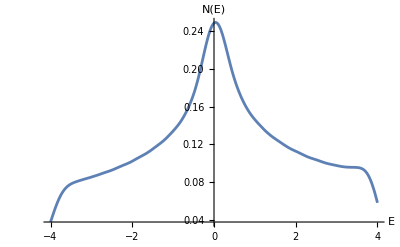

```mathematica
t=1.;
dirac[x_]:=1/(a Sqrt[Pi]) E^-(x/a)^2/. a->1/3

energy[kx_,ky_]:=-2 t (Cos[kx]+Cos[ky]);

nPoints=30;
kRange=Range[-Pi,Pi,2 Pi/(nPoints-1)];

energyValues=Flatten[Table[energy[kx,ky],{kx,kRange},{ky,kRange}]];

densityOfStates[Ee_]:=(1/Length[energyValues]) Sum[dirac[Ee-en],{en,energyValues}];

Plot[densityOfStates[Ee],{Ee,-4,4},PlotRange->All,AxesLabel->{"E","N(E)"},PlotRange->{{-4,4},{0,0.5}}]
```